# Bitcoin-USD Movements

This notebook serves to analyze Bitcoin price movements on either a daily, weekly, or monthly basis .

```mathematica
(* Since Mathematica operates in a global environment, let's clear all that, so we're clean *)
Clear["Global`"];
(* Buttons to hide / show code *)
CloseAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];SetOptions[#,CellOpen->False]&/@cells;];

OpenAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];SetOptions[#,CellOpen->True]&/@cells;];

Row[{Button["Hide Code",SelectionEvaluate[CloseAllInputsCells[]]],Button["Show Code",SelectionEvaluate[OpenAllInputsCells[]]]}]
```

Hide CodeShow Code

```mathematica
SetDirectory[NotebookDirectory[]];
settings=<|
imagemargins->20
,imagesize->1200
,labelstyle->{18}
,origindate->"Sep. 14, 2011"
,plotbackground->Lighter[LightGray,0.75]
,plotmarkers->{None,{"OpenMarkers",8},{"OpenMarkers",8}}
,plotstyle->{Automatic,Darker[Green],Lighter[Red]}
,subtitlestyle->{15}
,ticksstyle->{16}
,titlestyle->{20,Red}
|>;

(* Put these stats in the summary boxes placed within each plot *)
bstats[lst_]:=Return[<|
count->Length[lst]
,min->Min[lst]
,mean->Mean[lst]
,median-> Median[lst]
,max->Max[lst]
,std->StandardDeviation[lst]
|>//Dataset];

(* Time increment strings for selection *)
ly[str_]:=Switch[str,"Day","Daily","Week","Weekly","Month","Monthly","Year","Yearly"];
ticks2={#,PercentForm[Quantity[100 #,"Percent"]]}&/@Range[-1,1,1/10];
```

```mathematica
(* Here we fetch the data, and normalize it from a Dataset to a plain list *)
btcDataFull = FinancialData["BTC/USD", settings[origindate]]//Normal;
(* How many days data have we got? *)
days = btcDataFull//Length;

(* How much of the list do we take for display? *)
takes=MapIndexed[
#1->Style[ToString[First[#2]]<> " yr",16]&
,Join[
Range[365,days,365]
,{days}
]
]//ReverseSort;
```

```mathematica
(* The real fun begins here *)
Manipulate[
Module[
{filename}
,
(* insetscale places some of the inset stat boxes horizontally *)
insetscale={.07,.875};
intervally=ly[interval];
btcData=TimeSeriesAggregate[Take[btcDataFull,-since],interval,Last];
labelstyle={18};
updatedstr=Style[StringForm["(updated: ``)" , DateString[]],15];

(* A B S O L U T E   C H A N G E S *)
absolutechanges = Table[Last[btcData[[n]]]-Last[btcData[[n-1]]],{n,2, Length@btcData}];
tsabsolutechanges= TimeSeries[Table[{First[btcData[[n]]],Last[btcData[[n]]]-Last[btcData[[n-1]]]},{n,2, Length@btcData}]];
dlpabsolute=DateListPlot[
tsabsolutechanges
,PlotLabel->Column[
{
Style[
StringForm["Absolute `` Price Changes (USD)",intervally]
,settings[titlestyle]
]
,StringForm[
"`` ``s"
,Length[tsabsolutechanges["Values"]]
,interval
]
,updatedstr
}
,Center
]
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
,PlotRange->Full
,FrameTicks->All
, GridLines->Automatic
, Joined->False
,FrameLabel->{{HoldForm[US Dollars],None},{None,None}}
,LabelStyle->settings[labelstyle]
,Background->settings[plotbackground]
,Epilog->
Inset[
Framed[bstats[absolutechanges]]
,Scaled[insetscale]
,Background->White
]
];
filename = StringForm["BTC-USD-Movements-Absolute-``.jpg",intervally]//ToString;
Export[filename, dlpabsolute];
rankabs=SortBy[tsabsolutechanges//Normal,Last];
worstabs=Take[rankabs,Min[100,Length[rankabs]]]//Dataset;
bestabs=ReverseSortBy[Take[rankabs,Max[-100,-Length[rankabs]]],#[[2]]&]//Dataset;
worstandbestabs=Column[{
Style[
StringForm["Worst and Best ``s (Absolute Dollars)", interval]
,settings[titlestyle]
]
,updatedstr
,Row[{worstabs,bestabs}
,ImageSize->600
, Alignment->Center
]
}
,Alignment->Center
, Frame->True
];
filename = StringForm["BTC-USD-Movements-Best-Worst-Absolute-``.jpg",intervally]//ToString;
Export[filename,worstandbestabs];
(* R E L A T I V E   C H A N G E S *)
relativechanges = Table[
{
First[btcData[[n]]],(Last[btcData[[n]]]-Last[btcData[[n-1]]])/(Mean[{Last[btcData[[n]]],Last[btcData[[n-1]]]}])
}
,{n,2, Length@btcData}
];
tsrelativechanges = TimeSeries[relativechanges];
dlprelative=DateListPlot[
tsrelativechanges
,PlotLabel->Column[
{
Style[
StringForm["Relative `` Changes",intervally]
,settings[titlestyle]
]
,StringForm[
"`` ``s"
,Length[tsrelativechanges["Values"]]
,interval
]
,updatedstr
}
,Center
]
,PlotRange->All
,GridLines->{DateRange[{2011},{2030},"Year"],Range[-1,1,1/10]}
,Ticks->{Automatic,ticks2}
,FrameTicks->All
,Joined->False
,PlotMarkers->{Automatic,Scaled[0.005]}
,Filling->Axis
,FillingStyle->{Red, Green}
,Background->settings[plotbackground]
,ImageSize->settings[imagesize]
,LabelStyle-> settings[labelstyle]
,ImageMargins->settings[imagemargins]
,Epilog->
Inset[
Framed[bstats[tsrelativechanges["Values"]]]
,Scaled[insetscale]
,Background->White
]
];
filename = StringForm["BTC-USD-Movements-Relative-``.jpg",intervally]//ToString;
Export[filename, dlprelative];
rankrel=SortBy[tsrelativechanges//Normal,Last];
worstrel={#[[1]],#[[2]]//PercentForm}&/@Take[rankrel,Min[100,Length[rankrel]]]//Dataset;
bestrel=({#[[1]],#[[2]]//PercentForm}&/@ReverseSortBy[Take[rankrel,Max[-100,-Length[rankrel]]],#[[2]]&])//Dataset;
worstandbestrel=Column[{
Style[
StringForm["Worst and Best ``s (Relative)", interval]
,settings[titlestyle]
]
,updatedstr
,Row[{worstrel,bestrel}
,ImageSize->600
, Alignment->Center
]
}
,Alignment->Center
, Frame->True
];
filename = StringForm["BTC-USD-Movements-Best-Worst-Relative-``.jpg",intervally]//ToString;
Export[filename,worstandbestrel];
positives=Select[tsrelativechanges["Values"],#>0& ];
negatives=Select[tsrelativechanges["Values"],#<0& ];
mhistpositive=Histogram[
positives
,25
,PlotLabel->Column[
{
Style[
StringForm["Relative `` Positive Price Movements",intervally]
,settings[titlestyle]
]
,StringForm[
"`` of `` ``s"
,Length[positives]
,Length[positives] +Length[ negatives]
,interval
]
,updatedstr
}
,Center
]
,LabelStyle->settings[labelstyle]
,PlotRange->Full
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
,GridLines->Automatic
,Ticks->{ticks2, Automatic}
,FrameTicks->All
,ChartStyle->Green
,LabelingFunction->Above
,Background->settings[plotbackground]
,Epilog->Inset[
Framed[bstats[positives]]
,Scaled[{.50,.85}]
,Background->White
]
];
mhistnegative=Histogram[
{negatives}
,50
,PlotLabel->Column[
{
Style[
StringForm["Relative `` Negative Price Movements",intervally]
,settings[titlestyle]
]
,StringForm[
"`` of `` ``s"
,Length[negatives]
,Length[positives] +Length[ negatives]
,interval
]
,updatedstr
}
,Center
]
,LabelStyle->settings[labelstyle]
,PlotRange->Full
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
,GridLines->Automatic
,Ticks->{ticks2, Automatic}
,FrameTicks->All
,ChartStyle->Red
,LabelingFunction->Above
,LabelingFunction->Above
,Background->settings[plotbackground]
,Epilog->Inset[
Framed[bstats[negatives]]
,Scaled[{.50,.85}]
,Background->White
]
];
mhistcombined=Manipulate[
Histogram[{
positives,negatives}
,x
,PlotLabel->Column[
{
Style[
StringForm["Relative `` Movements",intervally]
,settings[titlestyle]
]
,StringForm[
"`` ``s"
,Length[positives] +Length[ negatives]
,interval
]
,updatedstr
}
,Center
]
,LabelStyle->settings[labelstyle]
,PlotRange->Full
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
,GridLines->{Range[-1,1,1/10],Automatic}
(*,Ticks->{ticks2, Automatic}*)
,FrameTicks->All
,ChartStyle->{Green, Red}
,LabelStyle->If[x>75,labelstyle,{labelstyle,Directive[If[x<50,12,8]]}]
,LabelingFunction->If[x>75,None,Above]
,Background->settings[plotbackground]
,Epilog->{
Inset[
Framed[bstats[Join[positives,negatives]]]
,Scaled[{.30,.90}]
,Background->White
]
,Inset[
Framed[bstats[negatives]]
,Scaled[{.10,.40}]
,Background->White
]
,Inset[
Framed[bstats[positives]]
,Scaled[{.90,.40}]
,Background->White
]
}
]
,{{x,50,Style["Bins: ",{15}]},Range[10,200,10]}
];
filename = StringForm["BTC-USD-Movements-Histogram-Relative-``.jpg",intervally]//ToString;
Export[filename,mhistcombined];
Column[{
Style[
StringForm["Absolute `` Movements",intervally]
,"Section"
]
,dlpabsolute
,worstandbestabs
,Spacer[10]
,Style[
StringForm["Relative `` Movements",intervally]
,"Section"
]
,dlprelative
,worstandbestrel
,mhistpositive
,mhistnegative
,mhistcombined
}
]
],
{
{interval,"Day"}
,#->Style[#,16]&/@{"Day", "Week","Month"}
}
, {
{since,days}
, takes
}
]
```

## Starting here to quantify price volatility (not ready for prime time yet)

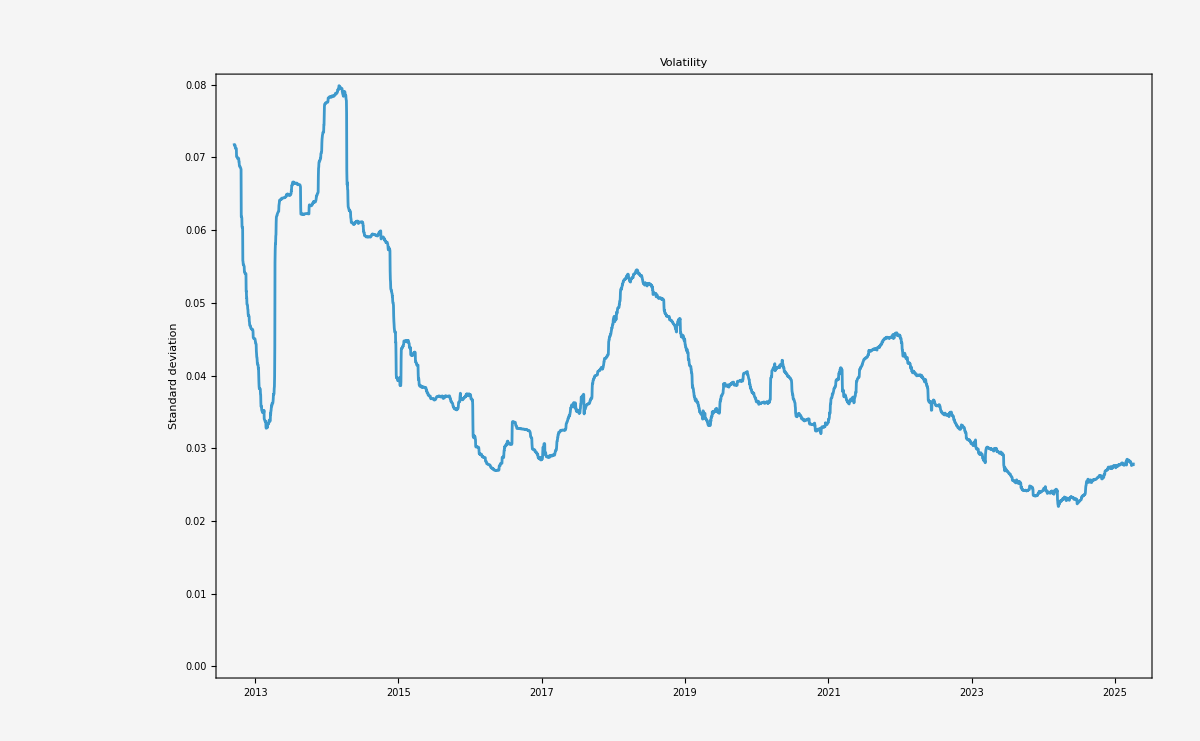

```mathematica
relativechangesall = Table[
{
First[btcDataFull[[n]]]
,(Last[btcDataFull[[n]]]-Last[btcDataFull[[n-1]]])/Mean[{Last[btcDataFull[[n]]],Last[btcDataFull[[n-1]]]}]
}
,{n,2, Length@btcDataFull}
];
tsrelativechangesall = TimeSeries[relativechangesall];
annualvolatility=MovingMap[StandardDeviation,tsrelativechangesall,Quantity[12,"Months"]];
DateListPlot[
annualvolatility
,PlotLabel->"Volatility"
,ImageSize->settings[imagesize]
,ImageMargins->settings[imagemargins]
,Background->settings[plotbackground]
,PlotRange->Full
,FrameTicks->All
,GridLines->{Automatic,Range[0,0.2,0.01]}
,FrameLabel->{{HoldForm[Standard deviation],None},{None,None}}
,LabelStyle->settings[labelstyle]
]
```